# Report Project II

Course code: IX1500
Date: 2018-10-04

Michel Ouadria, ouadria@kth.se
Rikard Jakobsson, rikjak@kth.se

Task 1: RSA cipher

## Summary

### Task

Professor Alice is sending a message to the student Bob according to the procedure in section Section.Subsection.4. You are supposed to crack the message. When translating to ASCII, you can assume the base 256.

```mathematica
nBob=126456119090476383371855906671054993650778797793018127;
eBob=7937;
```

```mathematica
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
```

The numbers is the list seems to be of the same size. Why?

### Result

p:255471513878248459929909589
q:494991074232809803525292243

The decrypted message:

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.

### Discussion

We read through the project 2 preparation guidance to get a better understanding of the problem. 

By finding the prime factors of nBob we were able to calculated the private keys of Bob, dBob. To get dBob we  need:
	Prime factors , pBob and qBob.
	Phi is the relatively prime factors of pBob and qBob,

It was fairly easy to decipher the code, this was due to the fact that we were given such a small size of nBob. The main problem with the code was getting q through a while loop.

### Conclusion

We were able to crack the code and retrieve the message. In a real scenario we wouldn’t be able to decipher the code this easily, since “nBob” wouldn’t be so small.

The numbers in the list are the same since we are splitting up the encrypted message into chunks. This is why we had to use StringJoin to merge all the split string.

## Code

```mathematica
ClearAll["`*"]
nBob=126456119090476383371855906671054993650778797793018127;(*Public key*)
eBob=7937;(*Bobs public key*)
B = 256;(*Base for the ascii*)

FactorInteger[nBob]
pBob = 494991074232809803525292243;(*One of the two prime factors of n*)
qBob = 255471513878248459929909589;(*Second of the two...*)
phi = (pBob-1)*(qBob-1);(*Phi of any prime number is -1 since no prime number has no factor greater than one*)
GCD[phi,eBob];
dBob = PowerMod[eBob,-1,phi];

cAlice={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};

(*mFromAlice=PowerMod[cAlice[[1]],dBob,nBob];*)
readMessage[x_]:=(
mFromAlice=PowerMod[x,dBob,nBob];
q=mFromAlice;ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
FromCharacterCode[ascii])
StringJoin[readMessage/@cAlice]
```

{{255471513878248459929909589,1},{494991074232809803525292243,1}}

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.

Task 2: RSA decryption analysis

## Summary

### Task

Write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the English text “ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.” for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits

Motivate your selected mathematical model!

### Result

### Discussion

### Conclusion

## Code

```mathematica
(*Bob wants to send a message to alice. He  pads it with m
Alice generates public and private key by generate a prime of same size, 100-200. 
Then, muliply to get n. 
Then to get Phi of n, (p-1)*(q-1)
Pick a small odd number that DOESN'T share a factor with Phi(N).
Finally, find d. 
*)
Remove["Global`*"];
B = 256;(*Base for the ascii*)
message = "ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.";
```

#### GenerateKeys

```mathematica
GenerateKeys[num_] := (
randP =NextPrime[RandomInteger[{2^num,2^(num+1)-1}]];
randQ =NextPrime[RandomInteger[{2^num,2^(num+1)-1}]];
n = randP*randQ;
ϕ = (randP-1)*(randQ-1);

rndForE:=RandomInteger[{2^4,2^6+ 1}]; 

While[GCD[e=rndForE,ϕ]≠1];
(*$keys ={"keyN"->n,"keyE"->e};*)
keys = {e,n}

)
```

#### RSAcrack

```mathematica
(*Crack the RSA*)
RSAcrack[cipher_,n_,e_]:=(
pq = FactorInteger[n];
     (*One of the two prime factors of n*)
p = pq[[1,1]];
q=pq[[2,1]];(*Second of the two...*)
phi = (p-1)*(q-1);(*Phi of any prime number is -1 since no prime number has no factor greater than one*)
GCD[phi,e];
d = PowerMod[e,-1,phi];
(*mFromAlice=PowerMod[cAlice[[1]],dBob,nBob];*)
```

#### Read message

```mathematica
readMessage[msg_]:=(
mFromAlice=PowerMod[msg,d,n];
qu=mFromAlice;
ascii={};
While[qu≠0,
AppendTo[ascii,Mod[qu,B]];
qu=Quotient[qu,B]
];
FromCharacterCode[ascii]);
StringJoin[readMessage/@cipher]
)
```

#### Encrypt message

```mathematica
(*Splits the provided string into smaller string chunks of the provided size*)
chunk[string_,partSize_]:=(StringCases[string,RegularExpression[".{1,"<>ToString[partSize]<>"}"]]);
(*Gets char code from the provided string using the n and e keys*)
charCode[msg_,n_,e_]:=(mess =ToCharacterCode[msg]. B^(Range[StringLength[msg]]-1);
mOut= PowerMod[mess,e,n])
(*Creates a cipher using the public keys*)
RSAencrypt[msg_,n_,e_]:=(
cipher ={};
chunkat=chunk[msg,4];
(charCode[#,n,e])&/@chunkat)

testMsg ="ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.";
(*test = RSAencrypt[testMsg,nnBob,eeBob];
RSAcrack[test,nnBob,eeBob]*)
listOfTiming = {};
testData = Range[50,100];

(*testTiming[time_]:=()*)
listOfTiming
```

#### All possible n bits

```mathematica
For[i= 50,i<101,i++, GenerateKeys[i];ee = keys[[1]];nn=keys[[2]];crypt = RSAencrypt[message,nn,ee];AppendTo[listOfTiming,{i,Timing[RSAcrack[crypt,nn,ee]][[1]]}]]
listOfTiming;

timeList ={{50,0.03978},{51,0.049216},{52,0.053028},{53,0.051833},{54,0.067854},{55,0.061266},{56,0.072162},{57,0.112672},{58,0.092},{59,0.098515},{60,0.135034},{61,0.104317},{62,0.120415},{63,0.136627},{64,0.196623},{65,0.182818},{66,0.20989},{67,0.204774},{68,0.30442},{69,0.430872},{70,0.487629},{71,0.532953},{72,0.637486},{73,0.465032},{74,1.001486},{75,0.999636},{76,1.114179},{77,0.966923},{78,3.338279},{79,3.911549},{80,3.924905},{81,5.207133},{82,4.345123},{83,6.770155},{84,8.547124},{85,9.443232},{86,10.13003},{87,8.31012},{88,11.359896},{89,12.573838},{90,16.345792},{91,16.090379},{92,18.726639},{93,25.41106},{94,24.511166},{95,42.877001},{96,55.379241},{97,50.707816},{98,68.04006},{99,104.666318},{100,107.593086}};
```

#### Plots

{a→0.162863,b→-11.8923}

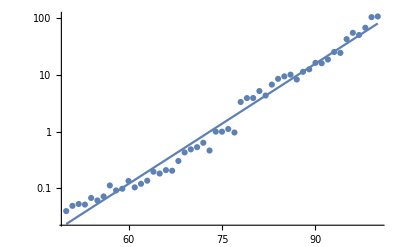

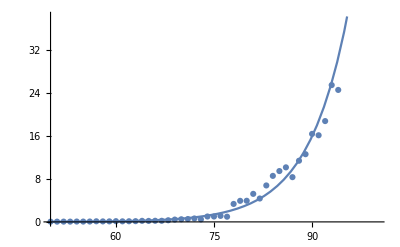

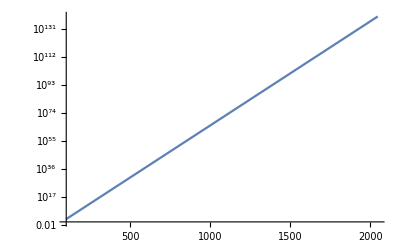

N = 4196 bits

4.91085×10^139

N = 2048 bits

1.83319×10^67

N = 1024 bits

1.12004×10^31

```mathematica
adder[in_]:=({in[[1]],Log[in[[2]]]});
tl=adder/@timeList;
timePlot=ListLogPlot[timeList];

fit=FindFit[tl,(a x+b),{a,b},x]
f[x_]:=E^(a*x+b)/.fit
plotlpot=LogPlot[f[x],{x,50,100}];
regPlot = Plot[f[x],{x,50,100}];
regTP = ListPlot[timeList];
Show[timePlot,plotlpot]
Show[regPlot,regTP]


plot2=LogPlot[f[k],{k,100,2048}]

"N = 4196 bits"
f[2048]
"N = 2048 bits"
f[1024]
"N = 1024 bits"
f[512]
```

## Summary

### Discussion

### Conclusion

## Code